# Mathematica ColorLibrary

## Jun Hirabayashi

jun@hirax.net http : // www.hirax.net

## Functions

### 設定変数

#### 表示・計算のための設定

```mathematica
Off[General::spell];
$RecursionLimit=$IterationLimit=2000;
```

#### 波長（領域・分割解像度）設定

```mathematica
(* 計算波長領域、および、グラフ表示などを行う場合に用いる波長分割幅 *)
(* 変更可能だが、計算を行なう過程では変更させない←計算速度などの兼ね合いでキャッシュしたい箇所も多々ある *)
MinWL = 350;
MaxWL = 800;
divWL=2;
```

### 標準光

#### D65スペクトル

```mathematica
D65 = Interpolation[{{350,0.4491},{351,0.4517456},{352,0.45378880000000005},{353,0.4553792},{354,0.45666640000000003},{355,0.45780000000000004},{356,0.45892960000000005},{357,0.4602048},{358,0.4617752},{359,0.46379040000000005},{360,0.46640000000000004},{361,0.47094400000000003},{362,0.47608400000000006},{363,0.48167200000000004},{364,0.48756},{365,0.4936},{366,0.500268},{367,0.5066360000000001},{368,0.5124000000000001},{369,0.517256},{370,0.5209},{371,0.5205960000000001},{372,0.51908},{373,0.516656},{374,0.513628},{375,0.5103},{376,0.5071136},{377,0.5042008},{378,0.5018311999999999},{379,0.5002744},{380,0.49979999999999997},{381,0.5028344},{382,0.5069511999999999},{383,0.5118808},{384,0.5173536},{385,0.5231},{386,0.524028},{387,0.525896},{388,0.52964},{389,0.536196},{390,0.5465},{391,0.5689792},{392,0.5952056},{393,0.6242424000000001},{394,0.6551528000000001},{395,0.687},{396,0.7181976},{397,0.7486208000000001},{398,0.7774952},{399,0.8040464},{400,0.8275},{401,0.8408864},{402,0.8511752},{403,0.8591408},{404,0.8655576},{405,0.8712000000000001},{406,0.881028},{407,0.890584},{408,0.899596},{409,0.907792},{410,0.9148999999999999},{411,0.9184720000000001},{412,0.9209559999999999},{413,0.922624},{414,0.9237479999999999},{415,0.9246},{416,0.9279288},{417,0.9309103999999999},{418,0.9331976000000001},{419,0.9344432},{420,0.9343000000000001},{421,0.9296464000000001},{422,0.9236032000000001},{423,0.9165168},{424,0.9087336},{425,0.9006000000000001},{426,0.8898543999999999},{427,0.8801032000000001},{428,0.8723448},{429,0.8675776000000001},{430,0.8668000000000001},{431,0.8789944},{432,0.8951792000000001},{433,0.9143568000000001},{434,0.9355296},{435,0.9577},{436,0.9768432},{437,0.9957455999999999},{438,1.0141664000000001},{439,1.0318648000000001},{440,1.0486},{441,1.062208},{442,1.074852},{443,1.086772},{444,1.0982079999999999},{445,1.1094},{446,1.1233592000000001},{447,1.1368616},{448,1.1494544},{449,1.1606848},{450,1.1701000000000001},{451,1.1736216000000002},{452,1.1753288000000002},{453,1.1756752000000001},{454,1.1751144},{455,1.1741},{456,1.1754984000000002},{457,1.1767471999999999},{458,1.1776967999999999},{459,1.1781976},{460,1.1781000000000001},{461,1.1760608000000001},{462,1.1734224},{463,1.1703336},{464,1.1669432000000002},{465,1.1634},{466,1.1598016},{467,1.1563608},{468,1.1532392},{469,1.1505984},{470,1.1486},{471,1.1486952},{472,1.1494336},{473,1.1506544},{474,1.1521968},{475,1.1539},{476,1.1562656},{477,1.1583048},{478,1.1596912000000001},{479,1.1600984},{480,1.1592},{481,1.1540616000000001},{482,1.1476168},{483,1.1401912},{484,1.1321104000000002},{485,1.1237000000000001},{486,1.1153592},{487,1.1073216000000001},{488,1.0998944},{489,1.0933848000000002},{490,1.0881},{491,1.0868016},{492,1.0867288000000002},{493,1.0875752},{494,1.0890344},{495,1.0908},{496,1.0916728},{497,1.0924624},{498,1.0930856},{499,1.0934591999999999},{500,1.0935},{501,1.0924624},{502,1.0910912},{503,1.0894688},{504,1.0876776},{505,1.0858},{506,1.0844752},{507,1.0830896},{508,1.0815864},{509,1.0799088000000001},{510,1.078},{511,1.0753488},{512,1.0724664},{513,1.0694096},{514,1.0662352},{515,1.063},{516,1.0590376000000001},{517,1.0553088},{518,1.0520512000000002},{519,1.0495024000000002},{520,1.0479},{521,1.0493792000000002},{522,1.0518056},{523,1.0549424},{524,1.0585528},{525,1.0624},{526,1.0662888},{527,1.0699304},{528,1.0730776},{529,1.0754832},{530,1.0769},{531,1.0751032},{532,1.0723175999999999},{533,1.0687904000000001},{534,1.0647688},{535,1.0605},{536,1.0567528},{537,1.0531224000000001},{538,1.0497256},{539,1.0466792},{540,1.0441},{541,1.0430392000000002},{542,1.0424456},{543,1.0422024},{544,1.0421928},{545,1.0423},{546,1.042532},{547,1.042616},{548,1.0424039999999999},{549,1.0417480000000001},{550,1.0405},{551,1.0373248},{552,1.0335584},{553,1.0293496},{554,1.0248472},{555,1.0202},{556,1.0160943999999998},{557,1.0120072},{558,1.0079528},{559,1.0039456},{560,1.},{561,0.9962520000000001},{562,0.992564},{563,0.98892},{564,0.9853040000000001},{565,0.9817},{566,0.9775224},{567,0.9734672000000001},{568,0.9696608000000001},{569,0.9662295999999999},{570,0.9633},{571,0.9620063999999999},{572,0.9612152},{573,0.9608008},{574,0.9606376000000001},{575,0.9606},{576,0.9611096000000001},{577,0.9613568000000001},{578,0.9610792000000001},{579,0.9600144},{580,0.9579000000000001},{581,0.9523744000000001},{582,0.9457992000000001},{583,0.9384368000000001},{584,0.9305496},{585,0.9224},{586,0.9139528},{587,0.9058423999999999},{588,0.8984056},{589,0.8919792},{590,0.8869},{591,0.8861992},{592,0.8868455999999999},{593,0.8885024},{594,0.8908327999999999},{595,0.8935},{596,0.8950984},{597,0.8966272},{598,0.8980168000000001},{599,0.8991975999999999},{600,0.9001000000000001},{601,0.9000944},{602,0.8998112},{603,0.8993208},{604,0.8986936},{605,0.898},{606,0.8978351999999999},{607,0.8976136},{608,0.8972743999999999},{609,0.8967568},{610,0.8959999999999999},{611,0.89446},{612,0.89268},{613,0.8907200000000001},{614,0.8886400000000001},{615,0.8865000000000001},{616,0.8850032},{617,0.8834056000000001},{618,0.8816064},{619,0.8795048},{620,0.877},{621,0.8731816000000001},{622,0.8689608},{623,0.8644392},{624,0.8597184},{625,0.8549},{626,0.8497272},{627,0.8447496},{628,0.8401584},{629,0.8361448},{630,0.8329000000000001},{631,0.8321448000000001},{632,0.8321584},{633,0.8327496},{634,0.8337272},{635,0.8349},{636,0.8359711999999999},{637,0.8368816},{638,0.8374664},{639,0.8375608},{640,0.8370000000000001},{641,0.8343008000000001},{642,0.8309464},{643,0.8271016},{644,0.8229312000000001},{645,0.8186},{646,0.8143208},{647,0.8101984},{648,0.8063856},{649,0.8030352000000001},{650,0.8003},{651,0.7995584000000001},{652,0.7994312000000001},{653,0.7997648000000002},{654,0.8004056},{655,0.8012},{656,0.8010760000000001},{657,0.8010280000000001},{658,0.801132},{659,0.8014640000000001},{660,0.8020999999999999},{661,0.8037272},{662,0.8056576},{663,0.8078144},{664,0.8101208},{665,0.8125},{666,0.8155344},{667,0.8183232},{668,0.8206248},{669,0.8221976000000001},{670,0.8228},{671,0.8202544},{672,0.8167392},{673,0.8124968},{674,0.8077696000000001},{675,0.8028000000000001},{676,0.7995296000000001},{677,0.7960768},{678,0.7922592},{679,0.7878944},{680,0.7828},{681,0.7753344},{682,0.7671392},{683,0.7583968},{684,0.7492896},{685,0.74},{686,0.7297664},{687,0.7199512},{688,0.7109728},{689,0.7032496},{690,0.6972},{691,0.6965928},{692,0.6976584},{693,0.6999776},{694,0.7031312},{695,0.7067},{696,0.7084471999999999},{697,0.7102256},{698,0.7120704000000001},{699,0.7140168},{700,0.7161},{701,0.7186336},{702,0.7213048000000001},{703,0.7240792},{704,0.7269224},{705,0.7298},{706,0.7350168000000001},{707,0.7396144},{708,0.7429736},{709,0.7444752},{710,0.7434999999999999},{711,0.7344784},{712,0.7229791999999999},{713,0.7096208},{714,0.6950216},{715,0.6798000000000001},{716,0.6636784},{717,0.6483952000000001},{718,0.6347928},{719,0.6237136000000001},{720,0.616},{721,0.6192272},{722,0.6258216},{723,0.6349424},{724,0.6457487999999999},{725,0.6574},{726,0.6661912},{727,0.6748616},{728,0.6832864},{729,0.6913408},{730,0.6989},{731,0.7048439999999999},{732,0.710292},{733,0.715368},{734,0.720196},{735,0.7249},{736,0.732772},{737,0.739976},{738,0.7458440000000001},{739,0.749708},{740,0.7509},{741,0.7434080000000001},{742,0.733244},{743,0.721076},{744,0.707572},{745,0.6934},{746,0.6828056000000001},{747,0.6719848},{748,0.6607112},{749,0.6487584},{750,0.6359},{751,0.6201016},{752,0.6033968000000001},{753,0.5860112000000001},{754,0.5681704},{755,0.5501},{756,0.5269152},{757,0.5052296},{758,0.4865464},{759,0.4723688},{760,0.4642},{761,0.47556240000000005},{762,0.4929352},{763,0.5148168},{764,0.5397056},{765,0.5661},{766,0.5903096},{767,0.6135688},{768,0.6349232},{769,0.6534184000000001},{770,0.6681},{771,0.6703784},{772,0.6688432000000001},{773,0.6644488},{774,0.6581496},{775,0.6509},{776,0.6467808},{777,0.6428384},{778,0.6392456},{779,0.6361752},{780,0.6338},{781,0.6336784},{782,0.6342512},{783,0.6353448},{784,0.6367856000000001},{785,0.6384000000000001},{786,0.6402416000000001},{787,0.6418528000000001},{788,0.6430032},{789,0.6434624},{790,0.643},{791,0.6395456},{792,0.6351688},{793,0.6300992},{794,0.6245664},{795,0.6188},{796,0.6130296000000001},{797,0.6074848},{798,0.6023952},{799,0.5979904},{800,0.5945}}] ;
```

### 補助標準光

#### D50光源スペクトル

```mathematica
D50 = Interpolation[{{300,0.02},{305,1.03},{310,2.05},{315,4.91},{320,7.78},{325,11.26},{330,14.75},{335,16.35},{340,17.95},{345,19.48},{350,21.01},{355,22.48},{360,23.94},{365,25.45},{370,26.96},{375,25.72},{380,24.49},{385,27.18},{390,29.87},{395,39.59},{400,49.31},{405,52.91},{410,56.51},{415,58.27},{420,60.03},{425,58.93},{430,57.82},{435,66.32},{440,74.82},{445,81.04},{450,87.25},{455,88.93},{460,90.61},{465,90.99},{470,91.37},{475,93.24},{480,95.11},{485,93.54},{490,91.96},{495,93.84},{500,95.72},{505,96.17},{510,96.61},{515,96.87},{520,97.13},{525,99.61},{530,102.1},{535,101.43},{540,100.75},{545,101.54},{550,102.32},{555,101.16},{560,100},{565,98.87},{570,97.74},{575,98.33},{580,98.92},{585,96.21},{590,93.5},{595,95.59},{600,97.69},{605,98.48},{610,99.27},{615,99.16},{620,99.04},{625,97.38},{630,95.72},{635,97.29},{640,98.86},{645,97.26},{650,95.67},{655,96.93},{660,98.19},{665,100.6},{670,103},{675,101.07},{680,99.13},{685,93.26},{690,87.38},{695,89.49},{700,91.6},{705,92.25},{710,92.89},{715,84.87},{720,76.85},{725,81.68},{730,86.51},{735,89.55},{740,92.58},{745,85.4},{750,78.23},{755,67.96},{760,57.69},{765,70.31},{770,82.92},{775,80.6},{780,78.27},{785,78.91},{790,79.55},{795,76.48},{800,73.4},{805,68.66},{810,63.92},{815,67.35},{820,70.78},{825,72.61},{830,74.44}}];
```

#### D55光源スペクトル

```mathematica
D55 = Interpolation[{{300,0.02},{305,1.05},{310,2.07},{315,6.65},{320,11.22},{325,15.94},{330,20.65},{335,22.27},{340,23.88},{345,25.85},{350,27.82},{355,29.22},{360,30.62},{365,32.46},{370,34.31},{375,33.45},{380,32.58},{385,35.34},{390,38.09},{395,49.52},{400,60.95},{405,64.75},{410,68.55},{415,70.07},{420,71.58},{425,69.75},{430,67.91},{435,76.76},{440,85.61},{445,91.8},{450,97.99},{455,99.23},{460,100.46},{465,100.19},{470,99.91},{475,101.33},{480,102.74},{485,100.41},{490,98.08},{495,99.38},{500,100.68},{505,100.69},{510,100.7},{515,100.34},{520,99.99},{525,102.1},{530,104.21},{535,103.16},{540,102.1},{545,102.53},{550,102.97},{555,101.48},{560,100},{565,98.61},{570,97.22},{575,97.48},{580,97.75},{585,94.59},{590,91.43},{595,92.93},{600,94.42},{605,94.78},{610,95.14},{615,94.68},{620,94.22},{625,92.33},{630,90.45},{635,91.39},{640,92.33},{645,90.59},{650,88.85},{655,89.59},{660,90.32},{665,92.13},{670,93.95},{675,91.95},{680,89.96},{685,84.82},{690,79.68},{695,81.26},{700,82.84},{705,83.84},{710,84.84},{715,77.54},{720,70.24},{725,74.77},{730,79.3},{735,82.15},{740,84.99},{745,78.44},{750,71.88},{755,62.34},{760,52.79},{765,64.36},{770,75.93},{775,73.87},{780,71.82},{785,72.38},{790,72.94},{795,70.14},{800,67.35},{805,63.04},{810,58.73},{815,61.86},{820,64.99},{825,66.65},{830,68.31}}];
```

#### D75光源スペクトル

```mathematica
D75 = Interpolation[{{300,0.04},{305,2.59},{310,5.13},{315,17.47},{320,29.81},{325,42.37},{330,54.93},{335,56.09},{340,57.26},{345,60},{350,62.74},{355,62.86},{360,62.98},{365,66.65},{370,70.31},{375,68.51},{380,66.7},{385,68.33},{390,69.96},{395,85.95},{400,101.93},{405,106.91},{410,111.89},{415,112.35},{420,112.8},{425,107.94},{430,103.09},{435,112.14},{440,121.2},{445,127.1},{450,133.01},{455,132.68},{460,132.36},{465,129.84},{470,127.32},{475,127.06},{480,126.8},{485,122.29},{490,117.78},{495,117.19},{500,116.59},{505,115.15},{510,113.7},{515,111.18},{520,108.66},{525,109.55},{530,110.44},{535,108.37},{540,106.29},{545,105.6},{550,104.9},{555,102.45},{560,100},{565,97.81},{570,95.62},{575,94.91},{580,94.21},{585,90.6},{590,87},{595,87.11},{600,87.23},{605,86.68},{610,86.14},{615,84.86},{620,83.58},{625,81.16},{630,78.75},{635,78.59},{640,78.43},{645,76.61},{650,74.8},{655,74.56},{660,74.32},{665,74.87},{670,75.42},{675,73.5},{680,71.58},{685,67.71},{690,63.85},{695,64.46},{700,65.08},{705,66.57},{710,68.07},{715,62.26},{720,56.44},{725,60.34},{730,64.24},{735,66.7},{740,69.15},{745,63.89},{750,58.63},{755,50.62},{760,42.62},{765,51.98},{770,61.35},{775,59.84},{780,58.32},{785,58.73},{790,59.14},{795,56.94},{800,54.73},{805,51.32},{810,47.92},{815,50.42},{820,52.92},{825,54.23},{830,55.54}}];
```

#### C光源スペクトル

```mathematica
C00 = Interpolation[{{{300,0.01},{305,0.01},{310,0.01},{315,0.01},{320,0.01},{325,0.2},{330,0.4},{335,1.55},{340,2.7},{345,4.85},{350,7},{355,9.95},{360,12.9},{365,17.2},{370,21.4},{375,27.5},{380,33},{385,39.92},{390,47.4},{395,55.17},{400,63.3},{405,71.81},{410,80.6},{415,89.53},{420,98.1},{425,105.8},{430,112.4},{435,117.75},{440,121.5},{445,123.45},{450,124},{455,123.6},{460,123.1},{465,123.3},{470,123.8},{475,124.09},{480,123.9},{485,122.92},{490,120.7},{495,116.9},{500,112.1},{505,106.98},{510,102.3},{515,98.81},{520,96.9},{525,96.78},{530,98},{535,99.94},{540,102.1},{545,103.95},{550,105.2},{555,105.67},{560,105.3},{565,104.11},{570,102.3},{575,100.15},{580,97.8},{585,95.43},{590,93.2},{595,91.22},{600,89.7},{605,88.83},{610,88.4},{615,88.19},{620,88.1},{625,88.06},{630,88},{635,87.86},{640,87.8},{645,87.99},{650,88.2},{655,88.2},{660,87.9},{665,87.22},{670,86.3},{675,85.3},{680,84},{685,82.21},{690,80.2},{695,78.24},{700,76.3},{705,74.36},{710,72.4},{715,70.4},{720,68.3},{725,66.3},{730,64.4},{735,62.8},{740,61.5},{745,60.2},{750,59.2},{755,58.5},{760,58.1},{765,58},{770,58.2},{775,58.5},{780,59.1},{785,59.1},{790,59.1},{795,59.1},{800,59.1},{805,59.1},{810,59.1},{815,59.1},{820,59.1},{825,59.1},{830,59.1}}];
```

### その他の光源

#### 白色光スペクトル(* 吸収スペクトル表示などで使う *)

```mathematica
whiteLight[ x_ ] = 1.0;
```

### 等色関数

#### CIE1986等色関数（スペクトル３刺激値）

```mathematica
xCIE1986ref = Interpolation[{ {350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0.0014},{385,0.0022},{390,0.0042},{395,0.0076},{400,0.0143},{405,0.0232},{410,0.0435},{415,0.0776},{420,0.1344},{425,0.2148},{430,0.2839},{435,0.3285},{440,0.3483},{445,0.3481},{450,0.3362},{455,0.3187},{460,0.2908},{465,0.2511},{470,0.1954},{475,0.1421},{480,0.0956},{485,0.058},{490,0.032},{495,0.0147},{500,0.0049},{505,0.0024},{510,0.0093},{515,0.0291},{520,0.0633},{525,0.1096},{530,0.1655},{535,0.2257},{540,0.2904},{545,0.3597},{550,0.4334},{555,0.5121},{560,0.5945},{565,0.6784},{570,0.7621},{575,0.8425},{580,0.9163},{585,0.9786},{590,1.0263},{595,1.0567},{600,1.0622},{605,1.0456},{610,1.0026},{615,0.9384},{620,0.8544},{625,0.7514},{630,0.6424},{635,0.5419},{640,0.4479},{645,0.3608},{650,0.2835},{655,0.2187},{660,0.1649},{665,0.1212},{670,0.0874},{675,0.0636},{680,0.0468},{685,0.0329},{690,0.0227},{695,0.0158},{700,0.0114},{705,0.0081},{710,0.0058},{715,0.0041},{720,0.0029},{725,0.002},{730,0.0014},{735,0.001},{740,0.0007},{745,0.0005},{750,0.0003},{755,0.0002},{760,0.0002},{765,0.0001},{770,0.0001},{775,0.0001},{780,0},{785,0},{790,0},{795,0},{800,0} }];
```

```mathematica
yCIE1986ref = Interpolation[{{350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0},{385,0.0001},{390,0.0001},{395,0.0002},{400,0.0004},{405,0.0006},{410,0.0012},{415,0.0022},{420,0.004},{425,0.0073},{430,0.0116},{435,0.0168},{440,0.023},{445,0.0298},{450,0.038},{455,0.048},{460,0.06},{465,0.0739},{470,0.091},{475,0.1126},{480,0.139},{485,0.1693},{490,0.208},{495,0.2586},{500,0.323},{505,0.4073},{510,0.503},{515,0.6082},{520,0.71},{525,0.7932},{530,0.862},{535,0.9149},{540,0.954},{545,0.9803},{550,0.995},{555,1},{560,0.995},{565,0.9786},{570,0.952},{575,0.9154},{580,0.87},{585,0.8163},{590,0.757},{595,0.6949},{600,0.631},{605,0.5668},{610,0.503},{615,0.4412},{620,0.381},{625,0.321},{630,0.265},{635,0.217},{640,0.175},{645,0.1382},{650,0.107},{655,0.0816},{660,0.061},{665,0.0446},{670,0.032},{675,0.0232},{680,0.017},{685,0.0119},{690,0.0082},{695,0.0057},{700,0.0041},{705,0.0029},{710,0.0021},{715,0.0015},{720,0.001},{725,0.0007},{730,0.0005},{735,0.0004},{740,0.0002},{745,0.0002},{750,0.0001},{755,0.0001},{760,0.0001},{765,0},{770,0},{775,0},{780,0},{785,0},{790,0},{795,0},{800,0}} ];
```

```mathematica
zCIE1986ref = Interpolation[{{350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0.0065},{385,0.0105},{390,0.0201},{395,0.0362},{400,0.0679},{405,0.1102},{410,0.2074},{415,0.3713},{420,0.6456},{425,1.0391},{430,1.3856},{435,1.623},{440,1.7471},{445,1.7826},{450,1.7721},{455,1.7441},{460,1.6692},{465,1.5281},{470,1.2876},{475,1.0419},{480,0.813},{485,0.6162},{490,0.4652},{495,0.3533},{500,0.272},{505,0.2123},{510,0.1582},{515,0.1117},{520,0.0782},{525,0.0573},{530,0.0422},{535,0.0298},{540,0.0203},{545,0.0134},{550,0.0087},{555,0.0057},{560,0.0039},{565,0.0027},{570,0.0021},{575,0.0018},{580,0.0017},{585,0.0014},{590,0.0011},{595,0.001},{600,0.0008},{605,0.0006},{610,0.0003},{615,0.0002},{620,0.0002},{625,0.0001},{630,0},{635,0},{640,0},{645,0},{650,0},{655,0},{660,0},{665,0},{670,0},{675,0},{680,0},{685,0},{690,0},{695,0},{700,0},{705,0},{710,0},{715,0},{720,0},{725,0},{730,0},{735,0},{740,0},{745,0},{750,0},{755,0},{760,0},{765,0},{770,0},{775,0},{780,0},{785,0},{790,0},{795,0},{800,0}} ];
```

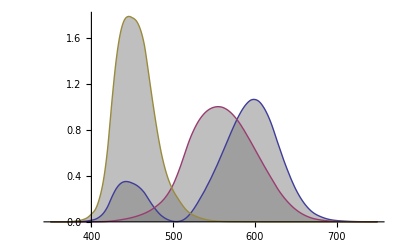

```mathematica
Plot[{xCIE1986ref[x],yCIE1986ref[x],zCIE1986ref[x]},{x,350,750},Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Gray]]
```

### 色度算出関数

#### CIE1986 「X Y Z 刺激値」計算関数(* “基準”なので白色光源に対するもの *)

(* XYZ刺激値計算コード  xCIE1986 などが定義されるまで動作しない *)

```mathematica
X1986[ spector_ ] := X1986[ spector ]= Block[{$Messages={}}, 
NIntegrate[ spector[x]  xCIE1986[x], {x,MinWL,MaxWL},WorkingPrecision→12, MaxRecursion->30] ];
```

```mathematica
Y1986[ spector_ ] := Y1986[ spector ] = Block[{$Messages={}}, 
NIntegrate[ spector[x]  yCIE1986[x], {x,MinWL,MaxWL},WorkingPrecision→12, MaxRecursion->30] ];
```

General::spell1: スペル間違いの可能性があります．新規シンボル"Y1986"はすでにあるシンボル"X1986"に似ています．

General::spell1: スペル間違いの可能性があります．新規シンボル"yCIE1986"はすでにあるシンボル"xCIE1986"に似ています．

```mathematica
Z1986[ spector_ ] := Z1986[ spector] = Block[{$Messages={}}, 
NIntegrate[ spector[x]  zCIE1986[x], {x,MinWL,MaxWL},WorkingPrecision→12, MaxRecursion->30] ];
```

#### 基準照明設定関数（ 返値は{ k, Xn, Yn, Zn } ）

```mathematica
setRefLight[ lightSpector_]:=
(RefLight = (lightSpector[#])&;

(* xCIE1986 などを光源スペクトルを使って作り直す *)
xCIE1986=(xCIE1986ref[#] RefLight[#])&; 
yCIE1986=(yCIE1986ref[#] RefLight[#])&; 
zCIE1986=(zCIE1986ref[#] RefLight[#])&; 

Xn0 = N[ X1986[ RefLight],4 ];　
Yn0 = N[ Y1986[ RefLight],4];
Zn0 = N[ Z1986[ RefLight],4 ];

{k = N[100 / Yn0, 4],
Xn = N[Xn0* k, 4],
Zn = N[Zn0 * k, 4], 
Yn = N[Yn0 * k, 4]} )
```

```mathematica
setRefLight[D65]; (* デフォルト値としてD65を設定 *)
```

#### Lab計算関数 ( 返値は{ L*, a*, b* } )

```mathematica
lab[ spector_ ]:=lab[ spector ]=
N[ {116( k Y1986[ spector ]/Yn)^(1/3)-16,
500 (( k X1986[ spector ]/Xn)^(1/3)-( k Y1986[ spector ]/Yn)^(1/3)),
200 (( k Y1986[ spector ]/Yn)^(1/3)-( k Z1986[ spector ]/Zn)^(1/3))} , 4]
```

#### 彩度計算関数 ( 返値は{ c* } )

```mathematica
c[ spector_ ]:=c[ spector ] = 
N[  Sqrt[
(500 (( k X1986[ spector ]/Xn)^(1/3)-( k Y1986[ spector ]/Yn)^(1/3)))^2+
(200 (( k Y1986[ spector ]/Yn)^(1/3)-( k Z1986[ spector ]/Zn)^(1/3)))^2], 4]
```

### 色フィルタ定義

#### 反射色スペクトル（吸収スペクトル） (* 命名ルールはhogeFilter *)

```mathematica
idealCyanFilter = Interpolation[ {{350,1-1},{400,1-1},{420,1-1},{440,1-1},{460,1-1},{480,1-1},{500,1-1},{520,1-1},{540,1-1},{560,1-1},{580,1-1},{600,1-0},{620,1-0},{640,1-0},{660,1-0},{680,1-0},{700,1-0},{800,1-0}}, InterpolationOrder->1];
```

```mathematica
idealMagentaFilter = Interpolation[ { {350,1-1},{400,1-1},{420,1-1},{440,1-1},{460,1-1},{480,1-1},{500,1-0},{520,1-0},{540,1-0},{560,1-0},{580,1-0},{600,1-0},{620,1-1},{640,1-1},{660,1-1},{680,1-1},{700,1-1},{800,1-1} }, InterpolationOrder->1];
```

```mathematica
idealYellowFilter = Interpolation[ { {350,1-0},{400,1-0},{420,1-0},{440,1-0},{460,1-0},{480,1-0},{500,1-0},{520,1-0},{540,1-1},{560,1-1},{580,1-1},{600,1-1},{620,1-1},{640,1-1},{660,1-1},{680,1-1},{700,1-1},{800,1-1} }, InterpolationOrder->1 ];
```

```mathematica
idealBlackFilter[x_] := 1;
```

```mathematica
cyanFilter = Interpolation[ 
{{350.000000,0.159000},{400.000000,0.159000}, {420.000000,0.089300}, {440.000000,0.052400}, {460.000000,0.031600}, {480.000000,0.023700}, {500.000000,0.024300}, {520.000000,0.042500}, {540.000000,0.098300}, {560.000000,0.237800}, {580.000000,0.424700}, {600.000000,0.543700}, {620.000000,0.607800}, {640.000000,0.552400}, {660.000000,0.445600}, {680.000000,0.439700}, {700.000000,0.517100}, {800,0.517100}}, InterpolationOrder->1];
```

```mathematica
magentaFilter = Interpolation[ 
{{350.000000,0.149900},{400.000000,0.149900}, {420.000000,0.135000}, {440.000000,0.124000}, {460.000000,0.143500}, {480.000000,0.196300}, {500.000000,0.276800}, {520.000000,0.428100}, {540.000000,0.568700}, {560.000000,0.644900}, {580.000000,0.596700}, {600.000000,0.133100}, {620.000000,0.042500}, {640.000000,0.021700}, {660.000000,0.016800}, {680.000000,0.014500}, {700.000000,0.009200}, {800.000000,0.009200}}, InterpolationOrder->1];
```

```mathematica
yellowFilter =Interpolation[ 
{{350.000000,0.668600},{400.000000,0.668600}, {420.000000,0.923400}, {440.000000,0.9800000}, {460.000000,0.901500}, {480.000000,0.644100}, {500.000000,0.180500}, {520.000000,0.072200}, {540.000000,0.044200}, {560.000000,0.031100}, {580.000000,0.022100}, {600.000000,0.018300}, {620.000000,0.013500}, {640.000000,0.009100}, {660.000000,0.008600}, {680.000000,0.008200}, {700.000000,0.004700}, {800.000000,0.004700}}, InterpolationOrder->1];
```

```mathematica
grayFilter[x_] := 0.99;
```

```mathematica
transparentFilter[x_] := 0.0;
```

### 色光源定義

#### 発光色スペクトル（発光スペクトル）関数 (* 命名ルールはhogeLight *)

```mathematica
blackLight[x_] = 0 ;
```

```mathematica
redLight[x_] =1.697085334713303 * ( 0.41844 xCIE1986[x] -0.15866 yCIE1986[x] -0.08283 zCIE1986[x]);
```

```mathematica
greenLight[x_] = 5.087234117636988 * ( -0.09117  xCIE1986[x] +0.25242  yCIE1986[x] +0.01570 zCIE1986[x]);
```

```mathematica
blueLight[x_] = 3.846060603242237 * (0.00092 xCIE1986[x] -0.00255  yCIE1986[x] +0.17858 zCIE1986[x]);
```

```mathematica
idealCyanLight=(1-idealCyanFilter [#])&;
```

```mathematica
idealMagentaLight=(1-idealMagentaFilter[#])&;
```

```mathematica
idealYellowLight=(1-idealYellowFilter[#])&;
```

```mathematica
idealBlackLight[x_] := 0;
```

```mathematica
cyanLight=(1-cyanFilter[#])&;
```

```mathematica
magentaLight=(1-cyanFilter[#])&;
```

```mathematica
magentaLight=(1-magentaFilter[#])&;
```

```mathematica
yellowLight=(1-yellowFilter[#])&;
```

### 色吸収計算

#### Lambert-Beer則による透過光関数 （滅法混色）

```mathematica
transmissionLight[ sourceLight_, layerFilter_, thinkness_ ] := transmissionLight[ sourceLight, layerFilter, thinkness] = Function[ {x}, 
sourceLight[x] (1-layerFilter[x])^(thinkness) ];
(* Lambert-Beer則による透過光スペクトル計算 *)
```

```mathematica
addLight[s1_,s2_,r1_,r2_]:= addLight[s1,s2,r1,r2] = Function[ {x}, 
(r1*s1[x]+r2*s2[x])/(r1+r2)];
(* スペクトルs1, s2を r1,r2の比率で足し合わせる　 ユーティリティ関数　*)
```

```mathematica
sumLight[spectors_]:=sumLight[spectors]=Function[{x},
(* 与えられたスペクトル群を全部足す。ユーティリティ関数 *)
Sum[ spectors[[i]][x],{i,1,Length[spectors]}]
];
```

```mathematica
meanLight[spectors_]:=meanLight[spectors]=Function[{x},
(* 与えられたスペクトル群の”平均” ユーティリティ関数　*)
Sum[ spectors[[i]][x],{i,1,Length[spectors]}]/Length[spectors]
];
```

```mathematica
ymckFilter[ sourceLight_, ymckValues_] := ymckFilter[ sourceLight, ymckValues] =
(* {Y量,M量,C量,K量}に対するトータルの吸収スペクトル *)
transmissionLight[
transmissionLight[
transmissionLight[ 
transmissionLight[sourceLight,yellowFilter,ymckValues[[1]]  ]
,magentaFilter,ymckValues[[2]]  ],
cyanFilter,ymckValues[[3]]   ],
grayFilter,ymckValues[[4]]   ] (* ymck = {{{y,m,c,k},{y,m,c,k},{y,m,c,k}.... *)
```

### スペクトル計算関数

#### スペクトル・色近似用関数

```mathematica
spectorFitting[s_, f1_, f2_, f3_] :=spectorFitting[s, f1, f2, f3]=
(* スペクトルsをスペクトルf1,f2,f3の線形和として近似する。返すのはf1,f2,f3に対する比率 *)
  {c1,c2,c3} /.
     NMinimize[
        { Apply[Plus,
            Table[  
              Abs[ s[x]   
                  - c1 f1[x]
                  - c2 f2[x]
                  - c3 f3[x] ],
              {x,MinWL+divWL,MaxWL-divWL ,divWL}] ]
          ,c1>0, c2>0, c3>0},
 {c1,c2,c3}
        ,AccuracyGoal -> 6, PrecisionGoal -> 6,MaxIterations -> 200][[2]];
(* rgb=spectorFitting[ (D65[#])&,redLight,greenLight,blueLight] *)
```

```mathematica
(* スペクトルsをスペクトルf1,f2,f3の線形和として近似し、近似したスペクトルを返す *)
```

```mathematica
fittingSpector[s_, f1_, f2_, f3_] :=fittingSpector[s, f1, f2, f3]  = (
  pars = {c1,c2,c3} /.
     NMinimize[
        {Apply[Plus,
            Table[  
              Abs[ s[x]   
                  - c1 f1[x]
                  - c2 f2[x]
                  - c3 f3[x] ],
              {x,MinWL+divWL,MaxWL-divWL ,divWL}] ]
          ,c1>0, c2>0, c3>0}, {c1,c2,c3}
        ,AccuracyGoal -> 6, PrecisionGoal -> 6,MaxIterations -> 200][[2]];
pars . {f1[#],f2[#],f3[#]}&
)
```

```mathematica
simpleRGB[s_]:=simpleRGB[s] = Clip[Re[{s[700],s[546],s[436]}],{0,1}];
(* 単純に436,546,700nmだけを抜き出し”RGB"とする関数（ざっくり表示に使う？） *)
```

#### 色表記変換

```mathematica
(* グラフ色表示用 のため面倒な計算は割愛版 *)
lab2xyz[lab_]:=lab2xyz[lab] = (
                  Module[ {x,y,z},
y=(lab[[1]]+16)/116;
x=lab[[2]] /500+y;
z=y-lab[[3]] /200;

N[{x,y,z}]*100
]
)
```

```mathematica
(* グラフ色表示用 のため面倒な計算は割愛版 *)
xyz2rgb[xyz_]:=xyz2rgb[xyz] = (
Module[{x,y,z,r,g,b},
x=xyz[[1]]/100;
y=xyz[[2]]/100;
z=xyz[[3]]/100;

r=x*3.2406+y*-1.5372+z*-0.4986;
g=x*-0.9689+y*1.8758+z*0.0415;
b=x*0.0557+y*-0.2040+z*1.0570;

r=If[r>0.0031308,1.055*(r^(1/2.4))-0.055,12.92*r]*255;
g=If[g>0.0031308,1.055*(g^(1/2.4))-0.055,12.92*g]*255;
b=If[b>0.0031308,1.055*(b^(1/2.4))-0.055,12.92*b]*255;

N[{r,g,b}]
]
)
```

```mathematica
(* グラフ色表示用 のため面倒な計算は割愛版 *)
lab2rgb[lab_]:=lab2rgb[lab] = xyz2rgb[ lab2xyz[ lab ] ]
```

### 表示関数

#### スペクトル・色表示用関数

```mathematica
(* 各波長に対する表示色をRGBで決定 *)
spectorColor[wl_]:= spectorColor[wl] = RGBColor[ 
Clip[ 3.240479 xCIE1986 [wl]  -1.537150  yCIE1986 [wl]  -0.498535  zCIE1986 [wl],{0,1}] ,
Clip[-0.969256  xCIE1986 [wl] +1.875992  yCIE1986 [wl]  +0.041556  zCIE1986 [wl],{0,1}] ,
Clip[+0.055648  xCIE1986 [wl] -0.204043  yCIE1986 [wl] +1.057311  zCIE1986 [wl] ,{0,1}]  ];
```

```mathematica
(* スペクトル表示関数 *)
spectorPlot[s_] := spectorPlot[s] = BarChart[  
Table[ s[x],{x,MinWL+50,MaxWL-100 ,divWL}],
GridLines->Automatic,
Frame->True,
FrameLabel->{"Wave Length","Intensity"},
FrameTicks->{None,Automatic},
ChartLabels->Table[ If[ Mod[x,50]==0,x,""],{x,MinWL+divWL,MaxWL-divWL ,divWL}],
ChartStyle->Table[ spectorColor[x],{x,MinWL+divWL+50,MaxWL-divWL-50 ,divWL}],
BarSpacing->-0.2,
(*ChartStyle->EdgeForm[None],*)
ChartBaseStyle->{Opacity[1.0],EdgeForm[None]},
Background->GrayLevel[1],
PlotRange->{0,1.2}]
```

```mathematica
<<"PolyhedronOperations`"
```

```mathematica
spectorLabPlot[spector_]:=( 
                  Module[ {labval,rgbval},
                          labval=lab[spector];
                          rgbval=Clip[Re[{spector[700],spector[546],spector[436]}],{0,1}];
                          Show[
                                Graphics3D[ 
                                           { RGBColor[ rgbval[[1]], rgbval[[2]], rgbval[[3]] ],
                                             Cuboid[ {labval[[1]]-2.5,labval[[2]]-5,labval[[3]]-5}, 
                                                     {labval[[1]]+2.5,labval[[2]]+5,labval[[3]]+5} 
                                                   ]
                                           }
                                          ],
                                Axes->True, AxesLabel->{"L*", "a*", "b*"}, 
                                FaceGrids->All, BoxRatios->{ 1, 1, 1 }, 
                                PlotRange->{{0,100},{-100,100},{-100,100}}, 
                                ViewPoint->{9.000, 0.000, 0.000},Lighting -> "Neutral"
                          ] 
                        ]
                      )
```

```mathematica
labPlot[labs_] := Show[ Graphics3D[ Table[ 
{ RGBColor[  xyz2rgb[ lab2xyz[labs[[i]]] ] /255
],
EdgeForm[Thin],
Cuboid[ {labs[[i]][[1]]-5/4,labs[[i]][[2]]-5/2,labs[[i]][[3]]-5/2}, 
{labs[[i]][[1]]+5/4,labs[[i]][[2]]+5/2,labs[[i]][[3]]+5/2} ]}
, {i, 1, Length[labs] }] ],
Axes->True, 
AxesLabel->{"L*", "a*", "b*"}, 
FaceGrids->All, 
BoxRatios->{ 1, 1, 1 }, 
PlotRange->{{0,100},{-100,100},{-100,100}},
ViewPoint->{9.000, 0.000, 0.000}
,Lighting -> "Neutral"]
```

```mathematica
labDeltaEPlot[labAnddeltaEs_] := Show[ Graphics3D[ Table[ 
{ RGBColor[ If[labAnddeltaEs[[i]][[2]]>1,1,0],
 0,
 If[labAnddeltaEs[[i]][[2]]>1,0,1]
],
EdgeForm[Thin],
Cuboid[ {labs[[i]][[1]]-5/4,labs[[i]][[2]]-5/2,labs[[i]][[3]]-5/2}, 
{labAnddeltaEs[[i]][[1]][[1]]+5/4,labAnddeltaEs[[i]][[1]][[2]]+5/2,labAnddeltaEs[[i]][[1]][[3]]+5/2} ]}
, {i, 1, Length[labs] }] ],
Axes->True, 
AxesLabel->{"L*", "a*", "b*"}, 
FaceGrids->All, 
BoxRatios->{ 1, 1, 1 }, 
PlotRange->{{0,100},{-100,100},{-100,100}},
ViewPoint->{9.000, 0.000, 0.000}
,Lighting -> "Neutral"]
```

#### 「画像」表示

```mathematica
YmckDensityPlot[ymckImages_]:=
{
ListDensityPlot[
ymckImages[[1]],
Mesh->False ,
ColorFunction->( (RGBColor[1,1,1-#])& )],
ListDensityPlot[
ymckImages[[2]],
Mesh->False ,
ColorFunction->( (RGBColor[1,1-#,1])& )],
ListDensityPlot[
ymckImages[[3]],
Mesh->False ,
ColorFunction->( (RGBColor[1-#,1,1])& )],
ListDensityPlot[
ymckImages[[4]],
Mesh->False ,
ColorFunction->( (RGBColor[1-#,1-#,1-#])& )]
}
```

```mathematica
rgbImageFromSpectorImage[spectorImage_]:= Module[
{width= Dimensions[spectorImage][[1]],height= Dimensions[spectorImage][[2]]},
Table[
spectorFitting[spectorImage[[x]][[y]], redLight, greenLight, blueLight ]
,{x,1,width},{y,1,height}
] ] (* スペクトル分布からRGB画像作成 *)
```

## Objective Oriented Definitions

### 各種公式・関数

#### フレネルの公式

```mathematica
(* θ=角度, n=媒質の屈折率 *)
```

```mathematica
Fresnel[θ_, n_] := Fresnel[θ, n]=N[(a=1/2(((Cos[θ]-√(n^2 - Sin[θ]^2))/(Cos[θ]+√(n^2 - Sin[θ]^2)))^2+((n^2  Cos[θ]-√(n^2 - Sin[θ]^2))/(n^2  Cos[θ]+√(n^2 - Sin[θ]^2)))^2);If[Im[a]≠0,1,a])]
```

#### スネルの法則による屈折ベクトルを計算する関数

```mathematica
angle2Normal[vec_]:=angle2Normal[vec]=N[ ArcCos[{vec[[1]],vec[[2]],Abs[ vec[[3]] ]}.{0,0,1}] ];
```

```mathematica
refractionVector[inVec_,normalVec_,r_]:=refractionVector[inVec,normalVec,r]=N[(w=(-(inVec.normalVec) r);t=1+(w-r)(w+r);k=√t; If[t>=0,r inVec+(w-k) normalVec,{inVec[[1]],inVec[[2]],-inVec[[3]]}])]
```

### クラス定義

#### 光追跡機能付きクラス

色 （スペクトル） にまつわる色々なものをひとつにまとめたクラス.
クラスのプロパティは"Spector"のみ. 
Module内で宣言した"self"を返すことで、Hoge[new] が呼ばれる毎に固有の関数・変数が定義され、各インスタンスを区別できる
(参考： 宮地 力「Mathematicaによるネットワークプログラミング」)

```mathematica
Spector[new]:=Module[
{Spector=D65,self},
self[set,spector_]:=(Spector=spector;self);
self[wavelength_]:=Spector[wavelength];
self[c]:=c[Spector];
self[spector]:=Spector;
self[lab]:=lab[Spector];
self[spectorPlot]:=spectorPlot[Spector];
self[toRGB]:=spectorFitting[Spector,redLight,greenLight,blueLight];
self[simpleRGB]:=simpleRGB[Spector];
self[labPlot]:=spectorLabPlot[Spector];
self]
```

General::spell1: スペル間違いの可能性があります．新規シンボル"Spector"はすでにあるシンボル"spector"に似ています．

General::spell1: スペル間違いの可能性があります．新規シンボル"set"はすでにあるシンボル"Set"に似ています．

光吸収を行う物体の層構成 にまつわるものをまとめたクラス.
クラスのプロパティは"Layers"のみ.
層構成の定義は, これまた"Layers"に「関数」として定義する.

```mathematica
Layer[new]:=Module[
{self, (* 屈折率,散乱率, 吸収スペクトル *)
                                          Layers=(Piecewise[{z=#[[3]];
                     {{1,0, Spector[new][set,transparentFilter]},z>1},
                     {{1,0, Spector[new][set,cyanFilter]},1≥ z&& z>0},
                     {{1,1, Spector[new][set,transparentFilter]},0≥ z}
                                        }  ])&
},
self[in,location_]:=Layers[location]=Layers[location];
self[spectorOf,location_]:=Layers[location][[3]];
self[set,layers_]:=(Layers=layers;self);
self]
```

General::spell1: スペル間違いの可能性があります．新規シンボル"Layers"はすでにあるシンボル"Layer"に似ています．

光吸収を行う層へ光をあてたときに、光経路とそのスペクトル変化をモンテカルロ法を用いてシミュレーションするクラス.
プロパティ"Trace"は, モンテカルロ法で光伝播を計算した時の経路(とその際のスペクトル)情報を保持する.

```mathematica
Light[new]:=Module[
{Spect=Spector[new],
Location={0,0,1.5},
UnitLength=0.01,
Vector=UnitLength*Normalize[{1,0.,-1}],
Trace={},
self},
self[setSpector,spector_]:=(Spect=spector;self);
self[setLocation,location_]:=(Location=location;self);
self[setVector,vector_]:=(Vector=vector;self);
self[set,spector_,position_,direction_]:=(Spect=spector;position=position;Direction=direction;self);
self[spector]:=Spect;
self[trace]:=Trace;
self[traceLocations]:=Table[Trace[[i]][[1]],{i,1,Length[Trace]}];
self[traceSpectrum]:=Table[Trace[[i]][[2]],{i,1,Length[Trace]}];
self[showSpectrum,step_]:=Table[Trace[[i]][[2]][spectorPlot],{i,1,Length[Trace],step}];
self[showTrace]:=(
arrows={};
Do[ rgb=Trace[[i-10]][[2]][simpleRGB];arrows=Join[arrows,{{Thickness[0.01],RGBColor[ rgb[[1]],rgb[[2]],rgb[[3]] ], 
        Line[ {{Trace[[i-10]][[1]][[1]],Trace[[i-10]][[1]][[2]],Trace[[i-10]][[1]][[3]]},
                                                               {Trace[[i]][[1]][[1]],Trace[[i]][[1]][[2]],Trace[[i]][[1]][[3]]}  }]  }} ],{i,11,Length[Trace],10}];
Show[  Graphics3D[  arrows, 
                                                Axes->True,AxesLabel->{"X","Y","Z"},
                                                AxesStyle->Directive[White,12],
                                                FaceGrids->All,BoxRatios->{40,40,15},                                   
                                                PlotRange->{{-2,2},{-2,2},{0,1.5}},
                                                ViewPoint->{9.000,0.000,0.000},
                                                Background->Black
 ]]
);
self[showSimpleTrace]:=(
arrows={};
Do[ arrows=Join[arrows,{{Thickness[0.001],RGBColor[ 0,0,0 ], 
        Line[ {{Trace[[i-1]][[1]][[1]],Trace[[i-1]][[1]][[2]],Trace[[i-1]][[1]][[3]]},
                                                               {Trace[[i]][[1]][[1]],Trace[[i]][[1]][[2]],Trace[[i]][[1]][[3]]}  }]  }} ],{i,2,Length[Trace],1}];
Show[  Graphics3D[  arrows, 
                                                Axes->True,AxesLabel->{"X","Y","Z"},
                                                FaceGrids->All,BoxRatios->{40,40,15},                                   
                                                PlotRange->{{-2,2},{-2,2},{0,1.5}},
                                                ViewPoint->{9.000,0.000,0.000}
 ]]
);
self[in,layer_]:=( Module[{n=0,r,
                                                       preLocationCondition={1,0, Spector[new][set,D65],1}
                                                        },
              While[n<1000 && Location[[3]]<=1.5,
                                 (*Print[{n,Location}];*)
                               (* boundary between layers *)
                                 If[ Location[[3]]<0.01,
                                      Location[[3]]=0.01;Vector=UnitLength*Normalize[{Random[]-0.5,Random[]-0.5,Random[]}],
                                      0
                               ];
                                f=Fresnel[ angle2Normal[100*Vector],r ];
                                ra=Random[];
                                 If[ r≠1, If[  Fresnel[ angle2Normal[100*Vector],r ]>ra,
                                                                 (*reflection*)
                                                                  Vector={Vector[[1]],Vector[[2]],-Vector[[3]]}, 
                                                                  (*reflaction*)
                                                                   If[Vector[[3]]<0,
                               Vector=0.01*Normalize[ refractionVector[100*Vector,{0,0,1},1/r]],
                               Vector=0.01*Normalize[ refractionVector[100*Vector,{0,0,-1},1/r]] ]  ], 
                                                        0]; 
                               (* scatter *)
                               Vector=If[ layer[in,Location][[2]]>Random[],
                                                         UnitLength*Normalize[Table[Random[]-0.5,{3}]], 
                                                         Vector  ] ;
                                r=layer[in,Location][[1]]/preLocationCondition[[1]];
                               preLocationCondition=layer[in,Location];
                                Spect=Spector[new][set, transmissionSpector[ Spect[spector], 
                                     layer[spectorOf,Location], UnitLength]   ];
                              Location=Location+Vector;     
                               If[r≠1,preLocationCondition=layer[in,Location],0];
                               Trace=Join[Trace,{{Location,Spect}}];
                               n=n+1;              
                      ]  
             ];self);
self]
```

## Samples

### Beer Color Sample

```mathematica
(* http://www.hirax.net/diaryweb/2012/08/16.html#10158 *)
```

```mathematica
j[x_,light_,halfThickness_,k_,s_]:=j[x,light,halfThickness,k,s]=(ⅇ^(√k √(k+2 s) (halfThickness-(-x))) light ((ⅇ^(2 √k √(k+2 s) (-x))-1) √k+(ⅇ^(2 √k √(k+2 s) (-x))+1) √(k+2 s)))/((ⅇ^(2 halfThickness  √k √(k+2 s))-1) √k+(ⅇ^(2  halfThickness  √k √(k+2 s))+1) √(k+2 s))
```

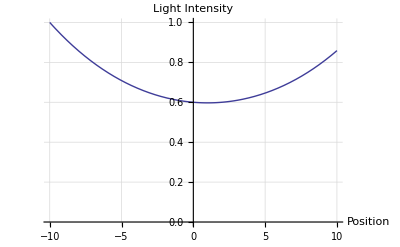

```mathematica
Plot[  {j[x,1,10,0.01,0.5]} ,{x,-10,10},PlotRange->{0,1},
GridLines->Automatic,
AxesLabel->{"Position","Light Intensity"}]
```

```mathematica
setRefLight[whiteLight];
```

```mathematica
aleColor=( redLight[#]/2. + greenLight[#]/2. )& ;
```

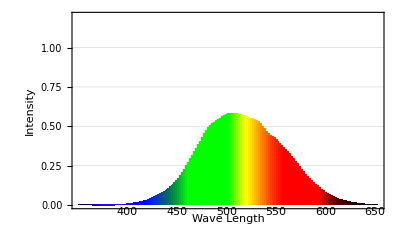

```mathematica
spectorPlot[ aleColor ]
```

```mathematica
lookingColor[ sourceLight_, halfThickness_,absorptionSpector_, s_ ] :=Function[ {x}, j[halfThickness,sourceLight[x],halfThickness,absorptionSpector[x],s]　 ];
```

```mathematica
spectors=Table[
lookingColor[ whiteLight, 10,(1-aleColor[#])/10&, s] ,
{s,0,0.5,0.1}
];
```

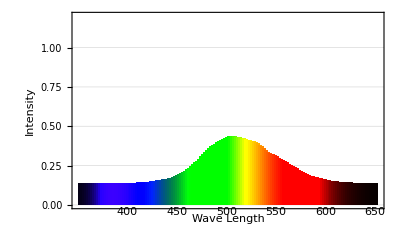
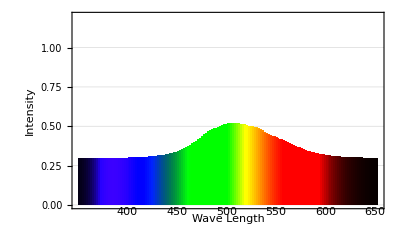
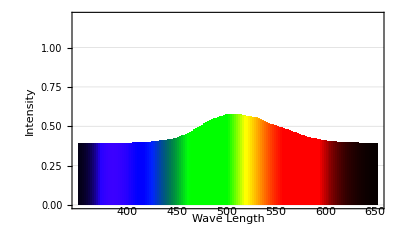
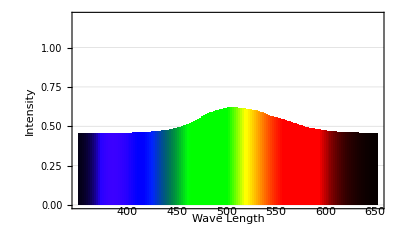
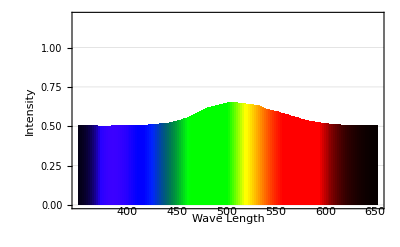
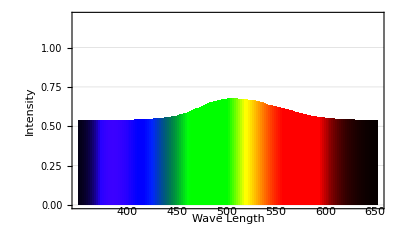

```mathematica
spectorPlot/@spectors
```

```mathematica
labPlot[lab/@spectors]
```

-Graphics3D-